```mathematica
DS=DSolve[{y'[t]==k*(y[t]-70),y[0]==300},y[t],t]
```

{{y[t]→10 (7+23 ⅇ^(k t))}}

```mathematica
y[t_]=DS[[1,1,2]];
S=NSolve[y[3]==200,k]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0.32651}}

```mathematica
y1[t_]=y[t]/.k->S[[1,1,2]]
```

0.32651 (-70+10 (7+23 ⅇ^(0.32651 t)))

```mathematica
Plot[y1[t],{t,0,70},PlotRange->{{0,75},{0,300}}]
```

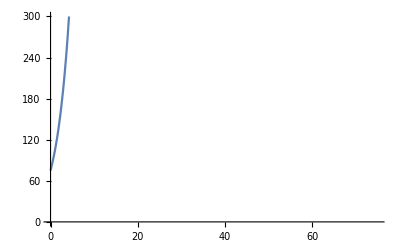

```mathematica
lst=Table[{t,y1[t]},{t,0,90,3}];
TableForm[lst,TableHeadings->{None,{"Time","Temp"}}]
```

Time | Temp
0 | 75.0974
3 | 200.
6 | 532.642
9 | 1418.54
12 | 3777.85
15 | 10061.2
18 | 26795.1
21 | 71360.9
24 | 190049.
27 | 506140.
30 | 1.34796×10^6
33 | 3.58989×10^6
36 | 9.56061×10^6
39 | 2.54619×10^7
42 | 6.78103×10^7
45 | 1.80593×10^8
48 | 4.80957×10^8
51 | 1.28089×10^9
54 | 3.41127×10^9
57 | 9.08492×10^9
60 | 2.4195×10^10
63 | 6.44364×10^10
66 | 1.71608×10^11
69 | 4.57027×10^11
72 | 1.21716×10^12
75 | 3.24154×10^12
78 | 8.6329×10^12
81 | 2.29912×10^13
84 | 6.12304×10^13
87 | 1.63069×10^14
90 | 4.34287×10^14